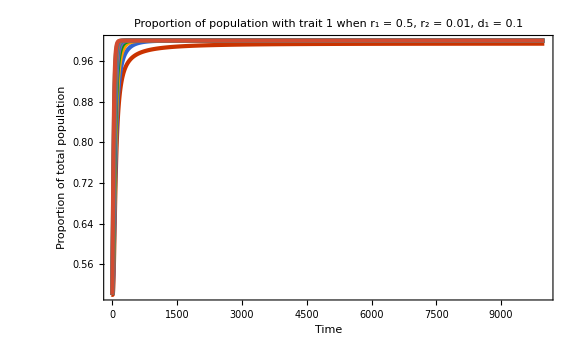

Image2.png

```mathematica
e1=(1-Subscript[d, 1])*(b/((Subscript[y, 1][s]+Subscript[y, 3][s])))*(Subscript[y, 1][s]*Subscript[y, 2][s]*Subscript[r, 1]+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*Subscript[r, 1]+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*Subscript[r, 2])-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 1][s];
e2=(1-Subscript[d, 1])*(b/((Subscript[y, 1][s]+Subscript[y, 3][s])))*(Subscript[y, 1][s]*Subscript[y, 2][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*(1-Subscript[r, 2]))-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 2][s];
e3=(1-Subscript[d, 2])*(b/((Subscript[y, 1][s]+Subscript[y, 3][s])))*(Subscript[y, 3][s]*Subscript[y, 4][s]*Subscript[r, 2]+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*Subscript[r, 1]+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*Subscript[r, 2])-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 3][s];
e4=(1-Subscript[d, 2])*(b/((Subscript[y, 1][s]+Subscript[y, 3][s])))*(Subscript[y, 3][s]*Subscript[y, 4][s]*(1-Subscript[r, 2])+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*(1-Subscript[r, 2]))-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 4][s];

(*FullSimplify[Solve[{e1==0,e2==0,e3==0,e4==0},{Subscript[y, 1][s],Subscript[y, 2][s],Subscript[y, 3][s],Subscript[y, 4][s]}]]*)

Subscript[r, 1] = 0.5;
Subscript[r, 2] = 0.01;
μ = 0.1;
b = 0.1;
Subscript[d, 1] = 0.1;
tmax = 10^4;
sol:= ParametricNDSolve[{Subscript[y, 1]'[s] == e1,Subscript[y, 2]'[s] == e2,Subscript[y, 3]'[s] == e3,Subscript[y, 4]'[s] == e4,Subscript[y, 1][0] == 0.1,Subscript[y, 2][0]== 0.1,Subscript[y, 3][0] == 0.1,Subscript[y, 4][0] == 0.1},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4]},{s,0,tmax},{Subscript[d, 2]}]

Plot[Evaluate@Table[(Subscript[y, 1][a][t]+Subscript[y, 2][a][t])/(Subscript[y, 1][a][t] + Subscript[y, 2][a][t]+Subscript[y, 3][a][t] + Subscript[y, 4][a][t])/.sol,{a,0.09,0.99,.1}],{t,0,tmax},PlotTheme -> "Web",PlotRange -> All,PlotLegends -> Placed[BarLegend[{"Rainbow",{0,1}},LegendLabel -> "value of d_2" ,LabelStyle -> Directive[Black,FontSize -> 12,FontFamily-> "Computer Modern"]],Below],AxesLabel->{"Time","Proportion of total population"},PlotLabel -> StringTemplate["Proportion of population with trait 1 when r_1 = `1`, r_2 = `2`, d_1 = `3`"][Subscript[r, 1],Subscript[r, 2],Subscript[d, 1]],ImageSize -> Large,LabelStyle->Directive[FontFamily->"Computer Modern",Black,FontSize->10]]

Export["Image2.png",Plot[Evaluate@Table[(Subscript[y, 1][a][t]+Subscript[y, 2][a][t])/(Subscript[y, 1][a][t] + Subscript[y, 2][a][t]+Subscript[y, 3][a][t] + Subscript[y, 4][a][t])/.sol,{a,0.01,0.99,.05}],{t,0,tmax},PlotTheme -> "Web",PlotRange -> All,PlotLegends -> Placed[BarLegend[{"Rainbow","Reverse"},LegendLabel -> "value of d_2" ,LabelStyle -> Directive[Black,FontSize -> 12,FontFamily-> "Computer Modern"]],Below],AxesLabel->{"Time","Proportion of total population"},PlotLabel -> StringTemplate["Proportion of population with trait 1 when r_1 = `1`, r_2 = `2`, d_1 = `3`"][Subscript[r, 1],Subscript[r, 2],Subscript[d, 1]],ImageSize -> Large,LabelStyle->Directive[FontFamily->"Computer Modern",Black,FontSize->10]]]


(*g1 = Evaluate[Table[sol[[1]][[2]][i][s],{i,0.1,0.9,0.1}]];
g2 = Evaluate[Table[sol[[2]][[2]][i][s],{i,0.1,0.9,0.1}]];
g3 = Evaluate[Table[sol[[3]][[2]][i][s],{i,0.1,0.9,0.1}]];
g4 = Evaluate[Table[sol[[4]][[2]][i][s],{i,0.1,0.9,0.1}]];*)


(*Plot[(g1+g2)/(g1+g2+g3+g4),{s,0,tmax},PlotRange -> All,AxesLabel->{"Time","Proportion of total population"},PlotStyle->Rainbow[1],PlotLegends -> Placed[BarLegend[{"Rainbow",{0.1,0.9}},LegendLabel -> "value of d_2" ,LabelStyle -> Directive[Gray,FontSize -> 12,FontFamily-> "Computer Modern"]],Below],ImageSize -> Large,LabelStyle->Directive[FontFamily->"Computer Modern",Gray,FontSize->12],PlotTheme -> "Web",PlotLabel -> StringTemplate["Proportion of population with trait 1 when r_1 = `1`, r_2 = `2`, d_1 = `3`"][Subscript[r, 1],Subscript[r, 2],Subscript[d, 1]]]

Export["Image1.png",Plot[(g1+g2)/(g1+g2+g3+g4),{s,0,tmax},PlotRange -> All,AxesLabel->{"Time","Proportion of total population"},PlotLegends -> Placed[BarLegend[{"Rainbow",{0.1,0.9}},LegendLabel -> "value of d_2" ,LabelStyle -> Directive[Gray,FontSize -> 12,FontFamily-> "Computer Modern"]],Below],ColorFunction -> "Rainbow",ImageSize -> Large,LabelStyle->Directive[FontFamily->"Computer Modern",Gray,FontSize->12],PlotTheme -> "Web",PlotLabel -> StringTemplate["Proportion of population with trait 1 when r_1 = `1`, r_2 = `2`, d_1 = `3`"][Subscript[r, 1],Subscript[r, 2],Subscript[d, 1]]]]
*)
(*g4 =sol[[1]][[4]][[2]];
g3 = sol[[1]][[3]][[2]];
g2 = sol[[1]][[2]][[2]];
g1 = sol[[1]][[1]][[2]];
Prop = (Evaluate[g1[s]]+Evaluate[g2[s]])/(Evaluate[g1[s]]+Evaluate[g2[s]] + Evaluate[g3[s]]+Evaluate[g4[s]]);
Prop2 =(Evaluate[g3[s]]+Evaluate[g4[s]])/(Evaluate[g1[s]]+Evaluate[g2[s]] + Evaluate[g3[s]]+Evaluate[g4[s]]);
Plot[{Prop,Prop2},{s,0,tmax},PlotRange -> All,AxesLabel->{"Time","Proportion of total population"},PlotLegends-> {"r_1 = 0.5, d_1 = 0.6","r_2 = 0.3, d_2= 0.3" },ImageSize -> Large]*)

(*Plot[(g3+g4)/(g1+g2+g3+g4),{s,0,1000}]*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Image1.png"]]]
```

Image1.png

Image1.png

Image1.png

«2 more identical outputs»

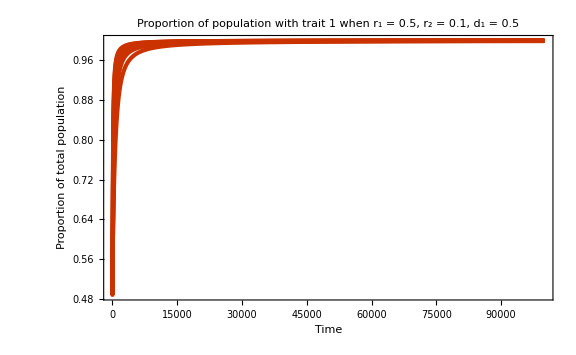

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

-Graphics-

Image1.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Image1.png"]]]
```